```mathematica
NotebookEvaluate["C:\\Users\\jonat\\Documents\\GitHub\\GeometricalPhyllotaxis\\Mathematica\\Packages\\CoinStacking.nb"];
SeedRandom[0];
```

## Cone parameters

```mathematica
SetDirectory[NotebookDirectory[]];

criticalConeArena[runID_,θ_,finalChainLength_] := Module[{arena,displayZ,displayConeArcLength,displayX},

(* length of topmost chain is  coneArcLength * 2 conesemiAngle *)
	displayConeArcLength=finalChainLength /(2 θ);
	displayZ=displayConeArcLength*Cos[θ];
	displayX=displayConeArcLength*Sin[θ];

	arena=<|
		"RunID"->runID,
		"Type"->"Cone",
		"DiskRadius"->1,
		"ConeSemiAngle"->θ,
		"LeftRotationMatrix"->RotationMatrix[2 θ],
		"RightRotationMatrix"->RotationMatrix[-2 θ],
		"Edges"-><|"Left"->InfiniteLine[{{0,0},{-Sin[θ],Cos[θ]}}],"Right"->InfiniteLine[{{0,0},{Sin[θ],Cos[θ]}}]|>,
		"zRange"->{0,displayZ},
		"Monitoring"->True,
		"DisplayRegion"->Disk[{0,0},displayConeArcLength,{π/2-θ,π/2+θ}],
		"RandomizationSeed"-> Missing[],
		"StoppingFunction"-> Function[run,run["ID"]>10000
		|| Max[#Polar["r"]&/@run["Disks"]]>displayConeArcLength]
	|>;
	arena =addInitialDisks[arena];
	arena
	];
```

## Do the run

```mathematica
coneArena=criticalConeArena["Test",N[π/8],40];
test11=doParameterisedRun[coneArena];
displayRun[test11]
```

Run  Test  273 	51.0797	33 	<|Up -> 19, Down -> 12|> 	Elapsed 4 s	Timing 31

-Graphics-

```mathematica
thetas=Range[π/8,π/4,0.01];
Print[Length[thetas]]
runs=MapIndexed[ criticalConeArena[First[#2],#1,55]&,thetas];
runs1=Map[doParameterisedRun,runs];
Export["runs1.mx",runs1];
```

40

Run  1  503 	70.0309	36 	<|Up -> 13, Down -> 21|> 	Elapsed 9 s	Timing 16

Run  2  490 	68.3401	36 	<|Up -> 13, Down -> 21|> 	Elapsed 9 s	Timing 16

Run  3  478 	66.6412	36 	<|Up -> 13, Down -> 21|> 	Elapsed 8 s	Timing 16

Run  4  468 	65.1021	36 	<|Up -> 13, Down -> 21|> 	Elapsed 12 s	Timing 47

Run  5  456 	63.5549	36 	<|Up -> 13, Down -> 21|> 	Elapsed 15 s	Timing 31

Run  6  446 	62.1209	36 	<|Up -> 13, Down -> 21|> 	Elapsed 10 s	Timing 47

Run  7  438 	60.7626	36 	<|Up -> 13, Down -> 21|> 	Elapsed 16 s	Timing 31

Run  8  429 	59.4728	36 	<|Up -> 21, Down -> 13|> 	Elapsed 17 s	Timing 47

Run  9  425 	58.2397	36 	<|Up -> 13, Down -> 21|> 	Elapsed 17 s	Timing 31

Run  10  422 	57.0857	36 	<|Up -> 21, Down -> 13|> 	Elapsed 17 s	Timing 31

Run  11  416 	55.8278	36 	<|Up -> 21, Down -> 13|> 	Elapsed 18 s	Timing 31

Run  12  421 	54.767	36 	<|Up -> 18, Down -> 16|> 	Elapsed 16 s	Timing 62

Run  13  422 	53.8667	37 	<|Up -> 15, Down -> 20|> 	Elapsed 18 s	Timing 47

Run  14  420 	52.6419	40 	<|Up -> 15, Down -> 23|> 	Elapsed 17 s	Timing 47

Run  15  404 	51.647	52 	<|Up -> 21, Down -> 29|> 	Elapsed 26 s	Timing 94

Run  16  395 	50.7012	52 	<|Up -> 24, Down -> 26|> 	Elapsed 24 s	Timing 62

Run  17  383 	49.7636	53 	<|Up -> 22, Down -> 29|> 	Elapsed 25 s	Timing 47

Run  18  372 	48.8752	46 	<|Up -> 25, Down -> 19|> 	Elapsed 23 s	Timing 94

Run  19  366 	48.147	47 	<|Up -> 22, Down -> 23|> 	Elapsed 25 s	Timing 78

Run  20  356 	47.2016	45 	<|Up -> 23, Down -> 20|> 	Elapsed 21 s	Timing 78

Run  21  345 	46.4514	45 	<|Up -> 18, Down -> 25|> 	Elapsed 19 s	Timing 78

Run  22  341 	45.6914	46 	<|Up -> 23, Down -> 21|> 	Elapsed 15 s	Timing 47

Run  23  331 	45.0926	42 	<|Up -> 20, Down -> 20|> 	Elapsed 13 s	Timing 31

Run  24  326 	44.1888	44 	<|Up -> 18, Down -> 24|> 	Elapsed 14 s	Timing 16

Run  25  321 	43.487	45 	<|Up -> 26, Down -> 17|> 	Elapsed 13 s	Timing 47

Run  26  315 	42.815	45 	<|Up -> 22, Down -> 21|> 	Elapsed 11 s	Timing 47

Run  27  310 	42.1368	45 	<|Up -> 25, Down -> 18|> 	Elapsed 9 s	Timing 31

Run  28  302 	41.5871	45 	<|Up -> 25, Down -> 18|> 	Elapsed 14 s	Timing 16

Run  29  294 	40.9704	36 	<|Up -> 13, Down -> 21|> 	Elapsed 11 s	Timing 47

Run  30  292 	40.4182	36 	<|Up -> 21, Down -> 13|> 	Elapsed 13 s	Timing 31

Run  31  294 	39.8909	45 	<|Up -> 23, Down -> 20|> 	Elapsed 13 s	Timing 31

Run  32  287 	39.1588	49 	<|Up -> 25, Down -> 22|> 	Elapsed 11 s	Timing 78

Run  33  283 	38.6553	45 	<|Up -> 23, Down -> 20|> 	Elapsed 14 s	Timing 78

Run  34  275 	38.1645	36 	<|Up -> 13, Down -> 21|> 	Elapsed 12 s	Timing 16

Run  35  276 	37.5732	44 	<|Up -> 26, Down -> 16|> 	Elapsed 13 s	Timing 47

Run  36  268 	37.0945	36 	<|Up -> 13, Down -> 21|> 	Elapsed 10 s	Timing 31

Run  37  269 	36.5707	45 	<|Up -> 23, Down -> 20|> 	Elapsed 12 s	Timing 31

Run  38  265 	36.0732	48 	<|Up -> 20, Down -> 26|> 	Elapsed 7 s	Timing 47

Run  39  263 	35.6186	41 	<|Up -> 23, Down -> 16|> 	Elapsed 5 s	Timing 31

Run  40  262 	35.2836	45 	<|Up -> 22, Down -> 21|> 	Elapsed 5 s	Timing 16

```mathematica
doneruns[[-1]]["Logging"]["ParastichyCount"]
```

```mathematica
zLoggingHeight[run_,id_] := Module[{res,mrd},
	mrd=run["Logging"]["Disks"][id];
	res=If[arenaConeQ[run["Arena"]],
		mrd["Polar"]["r"]
		,
		diskCentre[mrd["Disk"]][[2]]
		];
	res
];
zScaledHeight[run_,id_] := Module[{res},
res=zLoggingHeight[run,id];
If[arenaCylinderQ[run["Arena"]],Return[res]];
res= res * run["Arena"]["ConeSemiAngle"]
];
```

```mathematica
parastichyTraces[run_] := Module[{pc,pz},
pc=run["Logging"]["ParastichyCount"];
zValueLookup[id_] := run["Logging"]["Disks"][id];

pc=KeyValueMap[<|"DiskID"->#1,"Counts"->Sort[Values[#2]],"zHeight"->zScaledHeight[run,#1]|>&,pc];
pz= <|"Upper"->Map[ {#zHeight,Max[#Counts]}&,pc],"Lower"->Map[ {#zHeight,Min[#Counts]}&,pc]|>;
pz
];
lineParastichyTraces[run_]:= Module[{pc,pz},
pz=parastichyTraces[run];
{Line[pz["Upper"]],Line[pz["Lower"]]}
];

finalParastichy[run_] := Sort[Values[Last[run["Logging"]["ParastichyCount"]]]]
finalParastichyPoints[run_] := {
StandardRed,Point[{run["Arena"]["ConeSemiAngle"]/(π),finalParastichy[run][[1]]}],
StandardBlue,Point[{run["Arena"]["ConeSemiAngle"]/(π),finalParastichy[run][[2]]}]}
```

```mathematica
(*
thetas=Range[π/8,π/4,0.01];
Print[Length[thetas]]
runs=MapIndexed[ criticalConeArena[First[#2],#1,55]&,thetas];
runs1=Map[doParameterisedRun,runs];
Export["runs1.mx",runs1];
*)

coneThreshold1= Graphics[Map[finalParastichyPoints,runs1],AspectRatio->1,Axes->True,AxesOrigin->{0.1,0}];
```

```mathematica
Export["coneThreshold1.jpg",coneThreshold1]
```

```mathematica
thetas=Range[π * 0.14,π*0.18 ,0.001];
Print[Length[thetas]]
arenas2=MapIndexed[ criticalConeArena[First[#2],#1,55]&,thetas];
runs2=Map[doParameterisedRun,arenas2];
Export["runs2.mx",runs2];
coneThreshold1= Graphics[Map[finalParastichyPoints,runs2],AspectRatio->1,Axes->True,AxesOrigin->{0.1,0}];
```

coneThreshold1.jpg

```mathematica
runs1=doneruns;
```

-Graphics-

## Display

```mathematica
makeLine[run_,p_ <-> q_ , orientation_] :=  Module[{},
{orientationStyle[orientation],Line[{loggedDiskCentre[run,p],loggedDiskCentre[run,q]}]}
];


makeLines[run_] :=  Module[{chains,diskCentres},
chains=run["Logging"]["ChainStore"];
edgeSet=Join@@Flatten[Map[chainEdges[run,#]&,chains]];
KeyValueMap[makeLine[run,#1,#2]&,edgeSet]
];

makeTopChainLine[run_] :=  Module[{chains,diskCentres},
chains=Take[run["Logging"]["ChainStore"],-1];
edgeSet=Join@@Flatten[Map[chainEdges[run,#]&,chains]];
KeyValueMap[makeLine[run,#1,#2]&,edgeSet]
];
```

```mathematica
displayCone[arena_,rMinMax_] := Module[{xMin,xMax,zMin,zMax},
{xMin,xMax}=rMinMax*Sin[arena["ConeSemiAngle"]];
{zMin,zMax}=rMinMax*Cos[arena["ConeSemiAngle"]];
{{FaceForm[LightGreen],arena["DisplayRegion"]},
Line[{{xMin,zMin},{xMax,zMax}}]
,Line[{{-xMin,zMin},{-xMax,zMax}}]
,Circle[{0,0},rMinMax[[1]],{π/2-arena["ConeSemiAngle"],π/2+arena["ConeSemiAngle"]}]
,Circle[{0,0},rMinMax[[2]],{π/2-arena["ConeSemiAngle"],π/2+arena["ConeSemiAngle"]}]
}
];
```

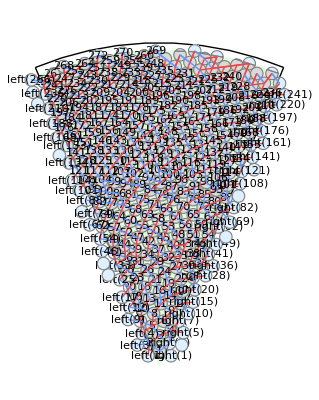

```mathematica
displayRun[test11]
```

```mathematica
lom[x_] := If[MissingQ[x],{},x];
labelledDisk[disk_] := {disk["Disk"],Text[disk["ID"],diskCentre[disk["Disk"]]]}
unlabelledDisk[disk_] := {disk["Disk"]}
tooltipDisk[disk_] := Tooltip[disk["Disk"],disk["ID"]];
```

```mathematica
emptyRegionQ[reg_] := Head[reg]===EmptyRegion;
regionDifferencer[region1_,region2_] := Module[{difference},
difference=RegionDifference[region1,region2];
If[Head[difference]==BooleanRegion,
	(* intersection did not work, hopefully because near to tangent *)
	difference=RegionDifference[DiscretizeRegion[region1],DiscretizeRegion[region2]]
];
difference 
];
regionIntersecter[region1_,region2_] := Module[{intersection},
intersection=RegionIntersection[region1,region2];
If[Head[intersection]==BooleanRegion,
	(* intersection did not work, hopefully because near to tangent *)
	intersection=RegionIntersection[DiscretizeRegion[region1],DiscretizeRegion[region2]]
];
intersection
];

diskInsideArenaQ[run_,disk_] :=
emptyRegionQ@ RegionWithin[run["Arena"]["DisplayRegion"],disk];
diskDisjointArenaQ[run_,disk_] := RegionDisjoint[
run["Arena"]["DisplayRegion"],disk];



diskPortionOutsideArena[run_,disk_Disk] := Module[{res},
If[diskInsideArenaQ[run,disk],Return[EmptyRegion[2]]];
If[RegionDisjoint[run["Arena"]["DisplayRegion"],disk],Return[disk]];
res=regionDifferencer[disk,run["Arena"]["DisplayRegion"]];
res
];


diskPortionInsideArena[run_,disk_Disk] := Module[{res},
If[diskInsideArenaQ[run,disk],Return[disk]];
If[diskDisjointArenaQ[run,disk],Return[EmptyRegion[2]]]; (* bug for adjoining regions *)

res=regionIntersecter[disk,run["Arena"]["DisplayRegion"]];
(*If[Head[res]==BooleanRegion,res=CanonicalizePolygon@DiscretizeRegion[res]
];
*)
res
]
```

```mathematica
diskNonIntersectingCylinderQ[run_,disk_Disk] := Module[{},
(
diskCentre[disk][[1]] >= run["Arena"]["CylinderCircumference"]/2+run["Arena"]["DiskRadius"]
||
 diskCentre[disk][[1]]<= -run["Arena"]["CylinderCircumference"]/2
-run["Arena"]["DiskRadius"])
];
diskNonIntersectingConeQ[run_,disk_Disk] := Module[{polar},
polar=disk2Polar[disk];
(
(
polar["θ"] >= run["Arena"]["ConeSemiAngle"]
&& RegionDistance[disk,run["Arena"]["Edges"]["Left"]]> run["Arena"]["DiskRadius"])
||
 diskCentre[disk][[1]]<= -run["Arena"]["CylinderCircumference"]/2
-run["Arena"]["DiskRadius"])
];
```

```mathematica
diskPortionInsideArena[run_,disk_Association] := diskPortionInsideArena[run,disk["Disk"]];
diskPortionOutsideArena[run_,disk_Association] := diskPortionOutsideArena[run,disk["Disk"]];
```

```mathematica
diskClassify[run_] := Module[{},

disks=Values[run["Logging"]["Disks"]];
leftEdgeDisks=leftShift[run["Arena"],#]&/@Select[disks,NumberQ[#ID]&& TrueQ[#CanSupportDisk["Right"]]&];
rightEdgeDisks=rightShift[run["Arena"],#]&/@Select[disks,NumberQ[#ID]&&TrueQ[#CanSupportDisk["Left"]]&];
visibleDisks=Join[
Select[disks,NumberQ[#ID]&],
leftEdgeDisks,
rightEdgeDisks];


croppedDisks=Map[Append[#,
<|
"Cropped"->diskPortionInsideArena[run,#],
"Exterior"->diskPortionOutsideArena[run,#]
|>
]&,visibleDisks];

If[globalShowNumbers,
	numbers=Map[Text[#ID,diskCentre[#Disk]]&,disks],numbers={}];


rimStyle=EdgeForm[Gray];

{{FaceForm[LightGray],rimStyle,#Cropped&/@croppedDisks}
,{FaceForm[LightBlue],rimStyle,#Exterior &/@croppedDisks},
numbers
}

];
```

```mathematica
displayRun[run_/; arenaConeQ[run["Arena"]]] := displayConeRun[run];
displayRun[run_/; arenaCylinderQ[run["Arena"]]] := displayCylinderRun[run];
```

```mathematica
displayCylinderRun[run_]:=Module[{cylinder,lines,topChainLines,disks,styledDisks,halfWidth,diskCentres,zRange},
cylinder={FaceForm[LightGreen],EdgeForm[None],run["Arena"]["DisplayRegion"]};

halfWidth=run["Arena"]["CylinderCircumference"]/2;
disks= Values[run["Logging"]["Disks"]];
diskCentres=diskCentre[#Disk]&/@disks;

zRange=MinMax[Last/@diskCentres];


styledDisks= diskClassify[run];

lines=makeLines[run];
topChainLines=makeTopChainLine[run];



Show[Graphics
[{
cylinder,
{InfiniteLine[{-halfWidth,0},{0,1}],InfiniteLine[{halfWidth,0},{0,1}]},
{styledDisks},
lines,
Thick,topChainLines,
displayDiskNumbers[run["Arena"],run["Logging"]["Disks"],Keys[run["Logging"]["Disks"]]]

},PlotRange->{3*{-halfWidth,halfWidth},zRange+{-run["Arena"]["DiskRadius"],run["Arena"]["DiskRadius"]}}]]
]
```

```mathematica
displayConeRun[run_]:=Module[{lines,topChainLines,disks,styledDisks,rMinMax},
disks= Values@run["Logging"]["Disks"];
rMinMax=MinMax[Map[#Polar["r"]&,disks]];
rMinMax=rMinMax+{-run["Arena"]["DiskRadius"],run["Arena"]["DiskRadius"]};
xMax=rMinMax[[2]]* Sin[run["Arena"]["ConeSemiAngle"]]+run["Arena"]["DiskRadius"];

styledDisks= diskClassify[run];

lines=makeLines[run];
topChainLines=makeTopChainLine[run];


graphics=
{
displayCone[run["Arena"],rMinMax],
{styledDisks},
lines,
Thick,topChainLines
(*displayDiskNumbers[arena,disks,Keys[disks]]
*)
};

Show[Graphics[graphics]
,PlotRange->{{-xMax,xMax},rMinMax+{-run["Arena"]["DiskRadius"],run["Arena"]["DiskRadius"]}}]
]
```

```mathematica
displayDiskNumbers[arena_,disks_,diskIDs_]:={ EdgeForm[{Thin,Gray}],FaceForm[Lighter[Blue,0.98]],
Map[displayDiskNumber[arena,disks,#]&,diskIDs]
};

displayDiskNumber[arena_,disks_,diskID_]:= Module[{disk},
disk=Lookup[disks,diskID]["Disk"];
{Text[diskID,diskCentre[disk]]}
];

segment[arena_,polar_] := Circle[{0,0},polar["r"],{π/2-1.5 arena["ConeSemiAngle"],π/2+1.5 arena["ConeSemiAngle"]}];
```

## Printout to scale

```mathematica
testScale[] := Module[{},
imageSizeInPoints=20*28.35;
g=testRun[15];
scale=Show[g,Graphics[{Thick,Black,Line[{{1,1},{2,1}}]}],Axes->True,PlotRange->{{-10,10},{0,29}}];
Export["graphic.pdf",g,ImageSize->imageSizeInPoints]
]
```